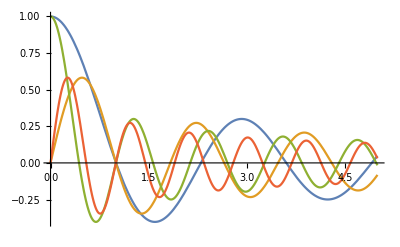

```mathematica
Plot[{BesselJ[0,2.40*x],BesselJ[1,3.83*x],BesselJ[0,5.52*x],BesselJ[1,7.02*x]},{x,0,5}]
```

I think that these functions might look very similar over the interval
500<r<505, because they will all be nearing zero. I think it will be very hard to differentiate them and they will essentially look like a y=0 line. But, let’s
find out!

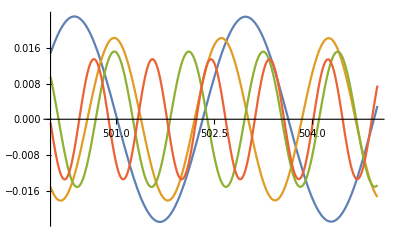

```mathematica
Plot[{BesselJ[0,2.40*x],BesselJ[1,3.83*x],BesselJ[0,5.52*x],BesselJ[1,7.02*x]},{x,500,505}]
```

So if you zoom in you can definitely see a difference, but they are all very close to zero. If I expand this out it looks like this:

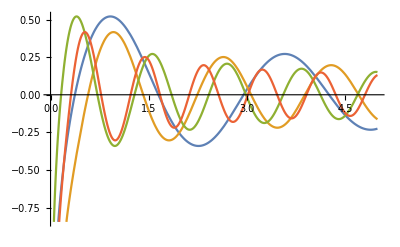

```mathematica
Plot[{BesselY[0,2.40*x],BesselY[1,3.83*x],BesselY[0,5.52*x],BesselY[1,7.02*x]},{x,0,5}]
```

Now we want roots at r = 1.

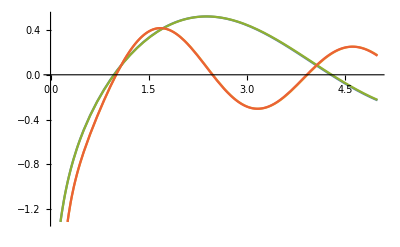

```mathematica
Plot[{BesselY[0,2.40/2.6*x],BesselY[1,3.83/1.75*x],BesselY[0,5.52/6*x],BesselY[1,7.02/3.2*x]},{x,0,5}]
```

Interesting, the Neumann Functions of the first kind become identical and the Neumann Functions of the second kind become identical when we place the roots are r = 1.

The Neumann functions are probably good for something. It does seem nice that functions of the same kind overlap so well at the root of r = 1. Being solutions to the circular wave equation is helpful, but that asymptote at 0 is a real stickler.